## Initialization

### Import dependencies

```mathematica
(* Run bubble-4a-murphree.nb before. *)
```

```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"}
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"}
```

C:\Users\josep\forschung\modeling\bubble_bec\mathematica_packages

C:\Users\josep\forschung\modeling\bubble_bec\output

```mathematica
If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]
```

```mathematica
Get["MovingTrap-murphree.m"]
Get["FitCurveHacked-mean-murphree.m"]
Get["SMThreeTraps.m"]
Get["SMThreeChipModel.m"]
```

The following variables used by ExpansionPlotHacked are protected by this package: {axis, trap, usemodel, frequency, trapposition, gridlines, size, meanfrequency, meanmodel}

### Define initial and final trap parameters

```mathematica
trapzero=(convertCALTableToTrapParameters@tableZLHb)⟦3;;⟧
```

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

```mathematica
trapone=(convertCALTableToTrapParameters@tableZHbB)⟦3;;⟧
```

{0.,2.6,2.6,-1.95,6.14298,-3.11336}

### Define target ramp analytic function

```mathematica
(*cass[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2 t^(1/4) -1)]/Tanh[5];
cassShort[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2(t/2)^(1/4) -1)]/Tanh[5];*)
```

```mathematica
(*omegaPlot=Plot[cassShort[800,50,t]^2,{t,0,1},PlotRange->All];
dOmegaPlot=Plot[Evaluate[(1/0.5)*Abs@D[cassShort[800,50,t],t]],{t,0,1},PlotRange->All,PlotStyle->{"Red"}];
Show[omegaPlot,dOmegaPlot,PlotRange->{{0,1},{0,6400}}]*)
```

```mathematica
(*periodT=0.250 (* [s] *);
omegaI=800 (* [Hz] *);
omegaF=20 (* [Hz] *);
Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->All,PlotStyle->{"Blue","Red"}]*)
```

```mathematica
(*Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->{{0,1},{0,1*10^4}},PlotStyle->{"Blue","Red"}]*)
```

```mathematica
(*
*)
```

```mathematica
(*num=20;
times={0,0.0085,0.017,0.024,0.032,0.04,0.047,0.056,0.068,0.095,0.127,0.142,0.157,0.172,0.189,0.208,0.233,0.267,0.33,0.4,1};
Length@times
Plot[Evaluate[D[cassShort[1,0,t],{t,1}]],{t,0,1},GridLines->{times,Table[-k*max/(num/2),{k,1,num/2}]}]*)
```

```mathematica
(*Length@Differences@times*)
```

```mathematica
(*Plot[cassShort[1,0,t],{t,0,1},GridLines->{times,{}},PlotRange->Full]*)
```

```mathematica
(*max=MaxValue[{Abs@Evaluate[D[cassShort[1,0,t],{t,1}]],t>0.01},t]*)
```

```mathematica
(*dCassShort[t_]=Evaluate[D[cassShort[1,0,t],{t,1}]];*)
```

```mathematica
(*(*InverseFunction@dCassShort*)*)
```

```mathematica
(*(*cassShortInv=InverseFunction@dCassShort*)*)
```

```mathematica
(*(*cassShortInv[-max]*)*)
```

```mathematica
(*Plot[Evaluate[D[cassShort[1,0,t],{t,2}]],{t,0,1},PlotRange->{{0,1},{-80,40}}]*)
```

```mathematica
(*corgierSimp[t_]:=Module[{tau=2*Pi*t},
(1/(12*Pi))*(6*tau-8*Sin[tau]+Sin[2*tau])];*)
```

```mathematica
(*Plot[1-corgierSimp[t],{t,0,1}]*)
```

```mathematica
(*Plot[Evaluate@D[1-corgierSimp[t],t],{t,0,1}]*)
```

```mathematica
(*InverseFunction[corgierSimp][8/3]*)
```

```mathematica
(*Plot[Evaluate@D[1-corgierSimp[t],{t,2}],{t,0,1}]*)
```

```mathematica
(*ArcCos[-1-2*Sqrt[2*6/10]]/(2*Pi)//N*)
```

```mathematica
(*trapAnalytic[trap1_,trap2_,t_]:=trap1+(trap2-trap1)*(1-cassShort[1,0,t]);
zeroCrossing[trap1_,trap2_]:=(1/8)*((1/5)*ArcTanh[2*Tanh[5]*((1/2)-trap2[[6]]/(trap2[[6]]-trap1[[6]]))]+1)^4;*)
```

```mathematica
(*Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All]
tauZero=zeroCrossing[trapzero,trapone]
period=500*10^(-3);
deltaTau=10*^-3/period;
newTaus={tauZero-deltaTau,tauZero,tauZero+deltaTau};
Print["tZero = "<>ToString[tauZero*period]]*)
```

```mathematica
(*Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,rampin1sguess⟦1⟧}]*)
```

```mathematica
(*Show[{
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All],
ListPlot[Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,Accumulate@rampin1sguess⟦1⟧}]]
}]*)
```

### Define ramp ansatz

#### Trap 1 Short

The first component of this object defines how to distribute the duration of each linear ramp in the ramp sequence. The durations are expressed as a fraction of the ramp sequence’s total duration, and so must sum to 1.

The second component of this object nominally is a guess at the fractional change of the ramp sequence for that linear ramp, but is not used by any of the fitting components and is considered vestigial.

```mathematica
rampin1sguess={2*{0.01,0.01,0.01,0.01,0.01,0.01,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.025,0.04,0.07,0.08,0.09},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

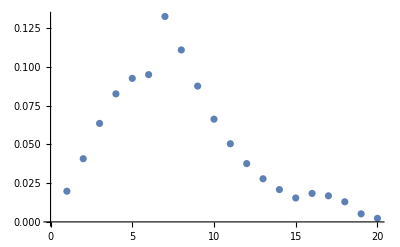

```mathematica
ListPlot[rampin1sguess⟦2⟧]
```

```mathematica
(*rampin1sguess⟦2,9;;13⟧
rampin1sguess⟦2⟧=Join[rampin1sguess⟦2,1;;9⟧,ConstantArray[0.,5],rampin1sguess⟦2,10;;⟧]*)
```

```mathematica
(*rampin1sguess*)
```

```mathematica
Total[rampin1sguess⟦1⟧]
```

```mathematica
Total[rampin1sguess⟦2⟧]
```

```mathematica
Length@rampin1sguess[[1]]
```

## Calculate ramp

The following took 8 1/2 minutes to complete. (1 1/4 hr on the Dell)

```mathematica
(* 
If FitCurveHacked runs in less than a second and has multiple errors citing GeometricMean, go back and make sure bubble-4a.nb was run before this notebook. MovingTrap-murphree.m calls ChipTrapFrequencies, which is defined in that notebook.
*)
```

```mathematica
nramps1short=Length@rampin1sguess⟦1⟧
(rampin1s=FitCurveHacked[trapzero,trapone,rampin1sguess,nramps1short,-3.5,-5,"CorgierSin"])//Timing
```

```mathematica
FindTrapEndpoints[trapzero,trapone]
```

```mathematica
startptsTest=Table[SingleTrapFrequency[trapzero,trapone,{{1},{1}},1,n],{n,2}];
```

```mathematica
startptsTest[[1,All]]
(ChipTrapFrequencies@@trapzero)[[4]]
```

```mathematica
GeometricMean@(startptsTest[[2,All]])
GeometricMean@((ChipTrapFrequencies@@trapone)[[4]])
```

```mathematica
GeometricMean[(ChipTrapFrequencies@@trapone)[[4]]]
```

```mathematica
corgierSin[t_,ωi_,ωf_]:=Module[{tau=2*Pi*t},
ωi+((ωf-ωi)/(12*Pi))*(6*tau-8*Sin[tau]+Sin[2*tau])];
```

```mathematica
Plot[corgierSin[t,1,0],{t,0,1}]
```

```mathematica
omegaMeanVF[trap0_,trap1_,fColl0_:0,fColl1_:1,deltaFColl_:0.1]:=Module[
{trapParametersVF=Table[trap0+(trap1-trap0)*fColl,{fColl,fColl0,fColl1,deltaFColl}],
omegasVF,omegaMeanVF},
omegasVF=Map[ChipTrapFrequencies@@#&,trapParametersVF];
Return[Map[GeometricMean[#[[4]]]&,omegasVF]];
];
```

```mathematica
fColl0=0.99;
fColl1=1;
deltaFColl=0.0005;
omegaMeans=omegaMeanVF[trapzero,trapone,fColl0,fColl1,deltaFColl]
```

```mathematica
ListPlot[MapThread[{#1,#2}&,{Table[fColl,{fColl,fColl0,fColl1,deltaFColl}],omegaMeans}]]
```

```mathematica
Beep[];
```

```mathematica
rampin1s⟦2⟧-rampin1sguess⟦2⟧
```

```mathematica
ListPlot[%,PlotRange->All]
```

The following took ~4 1/2 minutes to run. (~ 1 hr 12 min on Dell)

```mathematica
points1s=100;
(pts1s=MovingTrap[trapzero,trapone,rampin1s,points1s,nramps1short];)//Timing
```

```mathematica
Position[pts1s⟦All,1,1⟧,Min@pts1s⟦All,1,1⟧]
```

```mathematica
pts1s⟦31⟧
```

```mathematica
Length@pts1s
```

```mathematica
trapParamVt=RampList[trapzero,trapone,rampin1s,points1s,nramps1short];
```

```mathematica
trapParamVt[[31]]
```

### Plot calculated ramp’s parameters

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"z"]
```

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"x",meanfrequency->False]
```

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"y",meanfrequency->False]
```

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->False,frequency->False,gridlines->True,usemodel->True,size->Large,axis->"z",meanfrequency->True,meanmodel->True]
```

```mathematica
Beep[]
```

```mathematica
plotZFreqVZmin[movingtrap_]:=Module[{zs,omegas},
zs[n_]:=movingtrap⟦n,1,3⟧*10^6;
omegas[n_]:=movingtrap⟦n,2,3⟧;

ListPlot[Table[{zs[n],omegas[n]},{n,Range[Length[movingtrap]]}],Frame->True,FrameLabel->{"Trap z position (μm)","Trap z frequency (Hz)"}]
]
plotZFreqVZmin[pts1s]
```

```mathematica
plotFreqError[pts1s]
```

```mathematica
printTrapParameters[{{minx_,miny_,minz_},{omegax_,omegay_,omegaz_},bmin_}]:=Print[
"Position = "<>ToString[{minx,miny,minz}*10^6]<>" μm\n"<>
"Frequency = "<>ToString[{omegax,omegay,omegaz}]<>" Hz\n"<>
"Bmin = "<>ToString[bmin]<>" G"];

printTrapParameters[pts1s⟦1⟧]
printTrapParameters[pts1s⟦-1⟧]
```

```mathematica
plotTrapPrincAxes[trap1_,trap2_,rampin_]:=Module[
{nramps=Length@rampin⟦1⟧,
eVecIndex,
characVtime,
vec2Plot,vec3Plot},
characVtime=Table[SingleTrapCharacteristics[trap1,trap2,rampin,nramps,n],{n,nramps}];
eVecIndex=2;
vec2Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}],PlotMarkers->"OpenMarkers"];
eVecIndex=3;
vec3Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}]];
Show[vec2Plot,vec3Plot]
]
plotTrapPrincAxes[trapzero,trapone,rampin1s]
```

```mathematica
plotTrapYandZCharacteristics[movingramp_]:=Module[
{xFreqs=movingramp⟦All,2,1⟧,
yFreqs=movingramp⟦All,2,2⟧,
zFreqs=movingramp⟦All,2,3⟧,
xPlot,yPlot,zPlot},
xPlot=ListLogPlot[xFreqs,PlotStyle->Green];
yPlot=ListLogPlot[yFreqs,PlotStyle->Red];
zPlot=ListLogPlot[zFreqs,PlotStyle->Blue];
Show[yPlot,zPlot,xPlot,PlotRange->All]
]
plotTrapYandZCharacteristics[pts1s]
```

## Export ramp

### Export ramp

```mathematica
trap1short={#⟦1⟧,Table[Total[Take[Round[#⟦2⟧,10.^-5],n]],{n,Length@rampin1s⟦1⟧}]}&[rampin1s]
```

```mathematica
(* Set the DateStringFormat to help create unique names for each exported beam.The format is inspired by the ISO 8601 standard. *)
generateTimeStamp[]:=DateString[{"Year","Month","Day","T","Hour","Minute","Second"}];
rampTimeStamp=generateTimeStamp[]
```

```mathematica
Export[FileNameJoin@{outputDirectory,rampTimeStamp<>"_trap1short.csv"},trap1shortᵀ]
```

### Export ramp parameters

```mathematica
exportRampEndpoints[trap1_,trap2_,rampTimeStamp_,outputDirectory_]:=Module[
{
fileName=rampTimeStamp<>"_ramp_endpoints",
table={trap1,trap2},
headings={{"InitialTrap","FinalTrap"},{"IL[A]","IZ[A]","IH[A]","Bx[G]","By[G]","Bz[G]"}}
},
Print[table];
Export[FileNameJoin@{outputDirectory,fileName<>".csv"},table,TableHeadings->headings]
]

exportRampEndpoints[trapzero,trapone,rampTimeStamp,outputDirectory]
```

```mathematica
Beep[];
Pause[1];
Beep[];
```

```mathematica
defineTableFromTrap[trapone]
```

## Look at intermediate trap and CAL table values

```mathematica
listRampCALTables[trap1_,trap2_,rampin_,npoints_,nramps_:3]:=Module[
{
deltatrap=trap1-trap2,
ramp=Prepend[Table[{Sum[#[[1,i]],{i,n}],Sum[#[[2,i]],{i,n}],#[[2,n]]/#[[1,n]]},{n,nramps}]&[rampin],{0,0,0}],
ramplist,
colors={"Red","Orange","Yellow","Green","Blue","Black"}
},

ramplist=Prepend[Drop[Table[{t,Piecewise[Table[{#3-(#1[[n-1,2]]+#1[[n,3]]*(t-#1[[n-1,1]]))*#2,#1[[n-1,1]]<t<=#1[[n,1]]},{n,2,nramps+1}]&[ramp,deltatrap,trap1]]},{t,0.,1.,1./npoints}],1],{0.,trap1}];

Print[ToString[{#[[1]],#[[2,1]]}&/@ramplist]];

Return[Table[ListPlot[{#⟦1⟧*500,#⟦2,k⟧}&/@ramplist,PlotStyle->colors⟦k⟧],{k,6}]];
];
test=listRampCALTables[trapzero,trapone,rampin1s,points1s,nramps1short];
Show[test,PlotRange->All]
```

```mathematica
test[[6]]
```

```mathematica
rampin1s
```

```mathematica
plotRampCALTable[trap1_,trap2_,rampin_]:=Module[
{
deltaTrap=trap2-trap1,
totRamp=Table[{Total@rampin⟦1,1;;k⟧,Total@rampin⟦2,1;;k⟧},{k,Length@rampin⟦1⟧}]~Prepend~{0,0},
trapRamp
},
trapRamp=Table[(totRamp⟦k,2⟧*deltaTrap+trap1)~Prepend~totRamp⟦k,1⟧,{k,Length@rampin⟦1⟧+1}];
Return[trapRamp];
];
trapRamp=plotRampCALTable[trapzero,trapone,rampin1s]
trapzero
trapone
```

```mathematica
ListPlot[{#[[1]]*250,#[[7]]}&/@trapRamp]
```

```mathematica
Total@{1,2,3,4,5}
```